```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sandrews/SSA/INI/MMB paper/figures/MinDdimer

```mathematica
kad=0.37*10^-6
kda=0.05
kat=1.1*10^-6
kta=0.05
kdt=1.1*10^-6
ktd=0.37*10^-6
kdimer=8.5*10^-4
kdiss=1
khydro=1.2*10^-3
volume=1
maxtime=20
mindn=2000
atpc=N[930000/volume]
adpc=N[116000/volume]
```

3.7×10^-7

0.05

1.1×10^-6

0.05

1.1×10^-6

3.7×10^-7

0.00085

1

0.0012

1

20

2000

930000.

116000.

```mathematica
(* differential equations *)
eqa=an'[t]==kda*dn[t]+kta*tn[t]-an[t]*(kad*adpc+kat*atpc)+2*kdiss*aan[t]+kdiss*adn[t]+kdiss*atn[t]
eqd=dn'[t]==kad*an[t]*adpc+ktd*tn[t]*adpc-dn[t]*(kda+kdt*atpc)+2*kdiss*ddn[t]+kdiss*adn[t]+kdiss*dtn[t]
eqt=tn'[t]==kat*an[t]*atpc+kdt*dn[t]*atpc-tn[t]*(kta+ktd*adpc)+2*kdiss*ttn[t]+kdiss*dtn[t]+kdiss*atn[t]-2*kdimer*tn[t]*tn[t]
eqaa=aan'[t]==kda*adn[t]+kta*atn[t]-aan[t]*(2*kad*adpc+2*kat*atpc)-kdiss*aan[t]
eqdd=ddn'[t]==kad*adn[t]*adpc+ktd*dtn[t]*adpc-ddn[t]*(2*kda+2*kdt*atpc)-kdiss*ddn[t]+khydro*dtn[t]
eqtt=ttn'[t]==kat*atn[t]*atpc+kdt*dtn[t]*atpc-ttn[t]*(2*kta+2*ktd*adpc)-kdiss*ttn[t]+kdimer*tn[t]*tn[t]-2*khydro*ttn[t]
eqad=adn'[t]==2*kad*aan[t]*adpc+ktd*atn[t]*adpc+kta*dtn[t]+2*kda*ddn[t]-adn[t]*(kda+kdt*atpc+kat*atpc+kad*adpc)-kdiss*adn[t]+khydro*atn[t]
eqat=atn'[t]==2*kat*aan[t]*atpc+kdt*adn[t]*atpc+kda*dtn[t]+2*kta*ttn[t]-atn[t]*(kta+ktd*adpc+kad*adpc+kat*atpc)-kdiss*atn[t]-khydro*atn[t]
eqdt=dtn'[t]==2*kdt*ddn[t]*atpc+kat*adn[t]*atpc+kad*atn[t]*adpc+2*ktd*ttn[t]*adpc-dtn[t]*(ktd*adpc+kta+kda+kdt*atpc)-kdiss*dtn[t]+2*khydro*ttn[t]-khydro*dtn[t]
```

an'[t]==2 aan[t]+adn[t]-1.06592 an[t]+atn[t]+0.05 dn[t]+0.05 tn[t]

dn'[t]==adn[t]+0.04292 an[t]+2 ddn[t]-1.073 dn[t]+dtn[t]+0.04292 tn[t]

tn'[t]==1.023 an[t]+atn[t]+1.023 dn[t]+dtn[t]-0.09292 tn[t]-0.0017 tn[t]^2+2 ttn[t]

aan'[t]==-3.13184 aan[t]+0.05 adn[t]+0.05 atn[t]

ddn'[t]==0.04292 adn[t]-3.146 ddn[t]+0.04412 dtn[t]

ttn'[t]==1.023 atn[t]+1.023 dtn[t]+0.00085 tn[t]^2-1.18824 ttn[t]

adn'[t]==0.08584 aan[t]-3.13892 adn[t]+0.04412 atn[t]+0.1 ddn[t]+0.05 dtn[t]

atn'[t]==2.046 aan[t]+1.023 adn[t]-2.16004 atn[t]+0.05 dtn[t]+0.1 ttn[t]

dtn'[t]==1.023 adn[t]+0.04292 atn[t]+2.046 ddn[t]-2.16712 dtn[t]+0.08824 ttn[t]

```mathematica
soln=NDSolve[{eqa,eqd,eqt,eqaa,eqdd,eqtt,eqad,eqat,eqdt,
an[0]==2000,dn[0]==0,tn[0]==0,aan[0]==0,ddn[0]==0,ttn[0]==0,adn[0]==0,atn[0]==0,dtn[0]==0},
{an,dn,tn,aan,ddn,ttn,adn,atn,dtn},
{t,0,maxtime}];
```

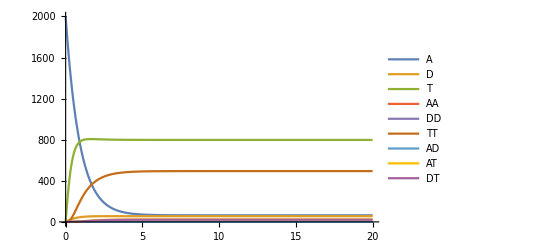

```mathematica
Plot[Evaluate[{an[t],dn[t],tn[t],aan[t],ddn[t],ttn[t],adn[t],atn[t],dtn[t]}/.soln],
{t,0,maxtime},
PlotLegends->{"A","D","T","AA","DD","TT","AD","AT","DT"},
PlotRange->{0,2000}]
```

```mathematica
(* Sort order: T, TT, A, D, AT, DT, AD, AA, DD *)eqvalues=First[Evaluate[{tn[maxtime],ttn[maxtime],an[maxtime],dn[maxtime],atn[maxtime],dtn[maxtime],adn[maxtime],aan[maxtime],ddn[maxtime]}/.soln]]
```

{797.976,494.527,64.0322,55.491,24.091,21.2324,0.697442,0.395748,0.307282}

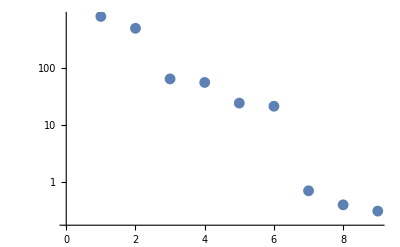

```mathematica
ListLogPlot[eqvalues]
```

```mathematica
(* Load and look at data *)
```

```mathematica
simdata=Import["minDdimerout.txt","CSV"];
```

```mathematica
simdata;
```

```mathematica
legend=simdata[[1]];
```

```mathematica
legend=Drop[legend,1]
```

{A,D,T,TT,TD,DT,TA,AT,AD,DA,AA,DD}

```mathematica
simdata=Drop[simdata,1];
```

```mathematica
plotdata=Table[Table[{simdata[[row,1]],simdata[[row,col]]},{row,Length[simdata]}],{col,2,Length[simdata[[1]]]}];
```

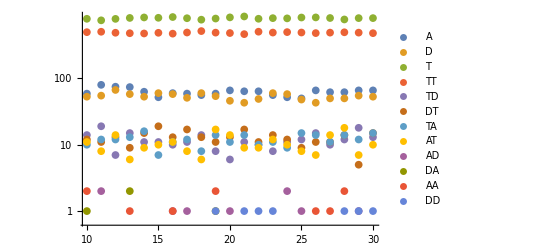

```mathematica
ListLogPlot[plotdata,PlotLegends->legend]
```

```mathematica
simdatat=Drop[Transpose[simdata],1];
```

```mathematica
legend
```

{A,D,T,TT,TD,DT,TA,AT,AD,DA,AA,DD}

```mathematica
(* Sort order: T, TT, A, D, AT, DT, AD, AA, DD *)simdata2=Transpose[{simdatat[[3]],simdatat[[4]],simdatat[[1]],simdatat[[2]],simdatat[[7]]+simdatat[[8]],simdatat[[5]]+simdatat[[6]],simdatat[[9]]+simdatat[[10]],simdatat[[11]],simdatat[[12]]}]
```

{{792,498,59,53,21,26,1,2,0},{751,505,80,55,20,30,2,0,0},{790,488,75,67,26,20,0,0,0},{816,480,74,58,19,24,2,1,0},{830,476,63,53,25,26,0,0,0},{820,487,52,60,17,30,0,0,0},{842,473,60,58,22,23,1,1,0},{808,492,59,51,20,28,1,0,0},{768,517,56,60,14,27,0,0,0},{799,490,59,54,31,19,1,2,1},{832,483,66,46,25,19,1,0,0},{859,465,64,43,23,28,0,0,1},{793,506,64,49,19,21,0,0,1},{810,491,56,60,23,22,0,0,1},{804,499,52,58,19,23,2,0,0},{828,492,50,48,23,21,1,0,0},{831,482,66,43,21,26,0,1,0},{814,490,62,50,25,21,0,1,0},{774,496,62,50,32,26,0,2,1},{811,490,66,55,19,23,1,0,1},{811,481,66,53,25,28,0,0,1}}

```mathematica
meandata=Mean[N[simdata2]]
```

{808.714,489.571,62.4286,53.5238,22.3333,24.3333,0.619048,0.47619,0.333333}

```mathematica
stddevdata=StandardDeviation[N[simdata2]]
```

{25.405,11.8599,7.59323,6.05491,4.29341,3.48329,0.740013,0.749603,0.483046}

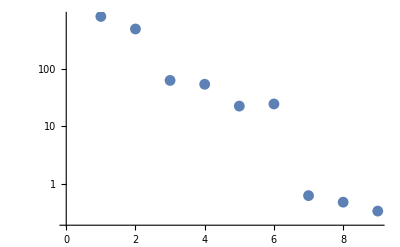

```mathematica
ListLogPlot[meandata]
```

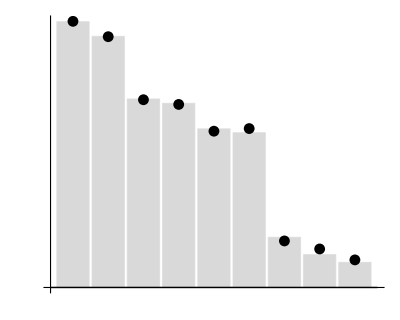

```mathematica
yshift=2;
Show[{BarChart[Log[eqvalues]+yshift,BarOrigin->Bottom,ChartStyle->LightGray,Ticks->None],
ListLogPlot[meandata*E^yshift,
PlotStyle->{Black}]},AspectRatio->0.8,AxesStyle->Bold]
```